# Lecture 9 - The Curious Case of Discontinuities

### A Puzzle...

#### Electron Jelly

Imagine a sphere of radius a filled with negative charge of uniform density, the total charge being equivalent to that of two electrons. Assume that two protons are embedded in this jelly, and further suppose that, in spite of their presence, the negative charge distribution remains uniform. Where must the protons be located so that the force on each of them is zero? 
(This is a surprisingly realistic caricature of a hydrogen molecule; the magic that keeps the electron cloud in the molecule from collapsing around the protons is explained by quantum mechanics!)

Solution
Recalling Gauss’s Law, the electric field at a distance r≤a from the center of the jelly sphere (which has charge density ρ=-(2e)/(4/3 π a^3)) equals E (4 π r^2)=1/ϵ_0(4/3 π r^3 ρ) or equivalently

E=(r ρ)/(3 ϵ_0)

A proton at a distance r would feel the force F_jelly=E e=(r |ρ| e)/(3 ϵ_0) pulling it towards the center of the jelly. To have stable equilibrium, the other proton must also be at a distance r on the same diameter as the first proton, but in the opposite direction. The repelling force between the two protons equals F_proton=(k e^2)/(2r)^2. Equilibrium occurs when F_jelly=F_proton, which allows us to solve for r,

(r |ρ| e)/(3 ϵ_0)=(k e^2)/(2r)^2
(r e)/(3 ϵ_0)(2e)/(4/3 π a^3)=(k e^2)/(2r)^2
r^3/a^3=1/8
r=a/2

In retrospect, this factor of 1/2 is clear. If all of the -2e electron charge were located in a point charge at the center, it would provide a force on one of the protons that is 8 times the force due to the other proton (because the other proton is twice as far away, and half as big). So the forces will balance if we reduce the effective electron charge by a factor of 8. This is accomplished by reducing the effective radius of the jelly by a factor of 2. □

### Advanced Electrostatics Problems

#### An Infinite Sheet

Example
An infinite sheet with uniform charge density σ lies in the x-y plane. What is the electric field E⃗ at all points in space?

Solution
We have built up a lot of mathematical machinery, so let’s solve this problem in four different ways:

Gauss’s Law: Exploit symmetry and use ∫E⃗·ⅆ a⃗=Q_enc/ϵ_0 to determine the electric field of the sheet

Coulomb’s Law: Consider the sheet to be comprised of uniformly charged rods, whose electric field we found in the last lecture is (E⃗)_rod=λ/(2π ϵ_0 r)r̂. Using Coulomb’s Law and the Principle of Superposition (E⃗=∫kⅆq/r^2 r̂), add up the electric fields of all the rods to determine the electric field from the sheet

Coulomb’s Law: The Principle of Superposition says that we can break up our charge distribution however we want, which grants us a lot of flexibility. Consider the sheet to be comprised of small patches of area (ⅆxⅆy) in Cartesian coordinates and sum up the electric field from each patch

Coulomb’s Law: Cartesian coordinates are sometimes not the optimal coordinate system. Consider the sheet to be comprised of small patches of area (rⅆrⅆθ) in polar coordinates and sum up the electric field from each patch

Method 1
By reflection symmetry, the electric field from the sheet must point in the z-direction, and by translational symmetry it can only depend upon the distance z from the sheet and not on the Cartesian coordinates x or y. In other words, E⃗=E[z]ẑ for z>0, and by symmetry E⃗=-E[z]ẑ for z<0.

We can exploit this symmetry by considering an (imaginary) cube with side length 2s that is split in two by the plane. As shown below, ⅆ â for this cube points in the x- or y-directions for four of the cube’s faces (the ones that get intersecting the x-y plane), whereas ⅆ â=ẑ for the top face and ⅆ â=-ẑ for the bottom face.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Since E⃗ points in the z-direction, the surface integral ∫E⃗·ⅆ a⃗ will be zero over the four faces intersecting the x-y plane. For the top face of the cube, ∫E⃗·ⅆ a⃗=∫(E[z]ẑ)·(ẑ ⅆ a⃗)=∫E[z]ⅆa. Similarly, for the bottom face ∫E⃗·ⅆ a⃗=∫(-E[z]ẑ)·(-ẑⅆ a⃗)=∫E[z]ⅆa. Therefore, Gauss’s Law yields

Q_enc/ϵ_0=∫E⃗·ⅆ a⃗=2∫_(top face) E[z]ⅆa=2E[z]∫_(top face) ⅆa=2E[z](2s)^2

where we have used the fact that the cube has side length 2s and hence area (2s)^2 on each face. The total charge Q_enc enclosed by the cube equals the charge of a square of side length 2s on the x-y plane, which is (2s)^2 σ. Substituting this above, we find

((2s)^2 σ)/ϵ_0=2E[z](2s)^2

E[z]=σ/(2 ϵ_0)

By exploiting the directionality of E⃗ discussed above and using symmetry, we find that the electric field at all points in space equals

E⃗=Piecewise[{{σ/(2 ϵ_0)ẑ, z>0}, {OverVector[0], z=0}, {σ/(2 ϵ_0)(-ẑ), z<0}}]

This is a remarkable result, and we will examine its implications below, but for now, let us verify this answer by computing the electric field in other ways.

Method 2
 If we split up the infinite sheet into thin rods of thickness ⅆx running parallel to the y-axis, their charge density would equal λ=σ ⅆx. The contribution of the electric field at our point in the z-direction would equal ⅆE=λ/(2π r ϵ_0)z/r where the last term picks out the z-component. Using r^2=x^2+z^2, the total electric field equals

E=∫_(-∞)^∞ σⅆx/(2π ϵ_0)z/(x^2+z^2)=(σ/(2π ϵ_0)ArcTan[x/z])_(x=-∞)^(x=∞)=σ/(2 ϵ_0)

as found above.

Method 3
We can always go back to good-old Coulombs Law! Consider a small patch of the surface at a point (x,y,0) with area ⅆxⅆy. The magnitude of the electric field at (0,0,z) from this patch equals ⅆE=kⅆq/r^2=(k(σⅆxⅆy))/(x^2+y^2+z^2). By symmetry, we know that the electric field must point in the z-direction, and hence we only want to pick out its z-component, which is (k(σⅆxⅆy))/(x^2+y^2+z^2)z/((x^2+y^2+z^2)^(1/2)). Integrating over all patches is nasty, but yields the correct solution

E=∫_(-∞)^∞ ∫_(-∞)^∞ (k(σⅆxⅆy))/(x^2+y^2+z^2)z/((x^2+y^2+z^2)^(1/2))=∫_(-∞)^∞ (2k σ zⅆy)/(y^2+z^2)=2π k σ=σ/(2 ϵ_0)

Method 4
Similar to Method 3, we now integrate over the x-y plane in polar coordinates. The magnitude of the electric field at (0,0,z) from a small patch at a point (r,θ) with area rⅆrⅆθ will be ⅆE=kⅆq/(r^2+z^2)=(k(σ rⅆrⅆθ))/(r^2+z^2). By symmetry, we know that the electric field must point in the z-direction, and hence we only want to pick out its z-component, which is (k(σ rⅆrⅆθ))/(r^2+z^2)z/((r^2+z^2)^(1/2)). Integrating over all patches is much nicer in polar coordinates (showing that it often helps to exploit symmetry and work in the most convenient coordinate system),

E=∫_0^(2π) ∫_0^∞ (k(σ rⅆrⅆθ))/(r^2+z^2)z/((r^2+z^2)^(1/2))=2π k σ=σ/(2 ϵ_0)

This quadruply confirms our result! □

Let’s take a second to admire this astounding result! No matter how far away you are from the shell, the electric field has the value σ/(2 ϵ_0) pointing away from the plane. Additionally, no matter how close you come to the plane, you still feel the electric field σ/(2 ϵ_0) pointing away from the plane. However, if you pass through the plane, the electric field will discontinuously change from σ/(2 ϵ_0) pointing in one direction to σ/(2 ϵ_0) pointing in the opposite direction! Furthermore, if you are a piece of charge embedded within the sheet, you will feel an electric field of 0 (by symmetry), but if you move an infinitesimal distance off the sheet you will feel an electric field of σ/(2 ϵ_0).

This type of behavior is only exhibited by infinitely thin sheets of charge. Volume charge distributions create continuous electric fields (since the integration in E⃗=∫(k ρⅆx'ⅆy'ⅆz')/r^2 r̂ smooths out discontinuities in ρ). And lines of charges don’t seem as alarming because the electric field goes to ∞ near the line of charge (just like for a point charge). So only 2D charge configurations have this bizarre behavior where the electric field is discontinuous but stays finite everywhere.

As stated in the "Field from a Cylindrical Shell, Right and Wrong" section in the previous lecture, a great rule to remember about discontinuities in nature is:

With all discontinuities in nature, the actual value at the discontinuity equals 
the average of the discontinuous values!

This statement is worth its weight in gold; print it on bumper stickers and share it with the world! You will see it come up again and again in physics (from charge distributions) and mathematics (Fourier series).

#### Intersecting Sheets

Example
Consider the cross section of three infinite sheets intersecting at equal angles. The sheets all have surface charge density σ.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

1. By adding up the fields from the sheets, find the electric field at all points in space.
2. Find the field instead by using Gauss’s law. You should explain clearly why Gauss’s law is in fact useful in this setup.
3. What is the field in the analogous setup where there are N sheets instead of three? What is your answer in the N→∞ limit?

Solution
1. The electric field form a given sheet points away from the sheet and has uniform magnitude σ/(2 ϵ_0). Therefore, in any of the 6 regions of space divided by the sheets, the electric field at every point in this region will be the same. Considering a point on the x-axis (i.e. directly to the right of the intersection point in the diagram above), the electric field from the nearest two sheets will be 2 σ/(2 ϵ_0)Sin[π/3]=σ/(2 ϵ_0) in the x-direction. The contribution of the third sheet will also be σ/(2 ϵ_0) in the x-direction, leading to an electric field in this entire region of σ/ϵ_0 in the x-direction. By radial symmetry, this is the magnitude of the electric field in all of the regions, with the direction of it appropriately rotated in each region.

2. We use for our Gaussian surface a regular hexagon centered on the intersection point of the sheet.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Assume that the length of the Gaussian surface between two sheets is l and that its depth (going into and our of the page) is d. Because the electric field points perpendicularly outwards against our Gaussian surface, Gauss’s Law yields

E (6 l d)=((6 l d)σ)/ϵ_0

or equivalently E=σ/ϵ_0, as found above. Note that while Gauss’s Law is always valid, it is only useful when you can find a simple surface that is everywhere perpendicular to the electric field and where the electric field has a uniform value.

3. For general N, we use Gauss’s Law (or, for the mathematically minded, set up a summation over pairs of electric sheets as we did in the first part of this problem) using a regular 2N-gon with side length l and depth d. The surface area of this 2N-gon is (2N)(2 Sin[π/(2N)])l d and the charge enclosed is (2N)l d σ. So Gauss’s Law yields

E (2N l d)=(σ(2N)d)/ϵ_0 l/(2Sin[π/(2N)])

or equivalently E=σ/(2 ϵ_0 Sin[π/(2N)]). As expected, this is independent of r. And it agrees with the above result when N=3. For large N, Sin[π/(2N)]≈π/(2N) so E≈N/π σ/ϵ_0. In the case of large N, the sheets are very close to each other, so we effectively have a continuous volume charge distribution that depends on r. The separation between adjacent sheets grows linearly with r, so we have ρ[r]∝1/r. More precisely, you can easily show that ρ[r]=(N σ)/(π r). As a simple exercise, you can use Gauss’s Law to easily show that for a volume charge distribution with cylindrical symmetry and a constant electric field that is independent of r, we must have ρ[r]∝1/r. □

#### Hole in a Shell

Example
Consider a spherical shell of charge, of radius R and surface charge density σ, from which a small circular piece of radius b≪R has been removed.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

We know that for a complete spherical sheet (the b=0 limit), there will be a discontinuity in the electric field when we go from just inside to just outside the sphere. Once we remove this infinitesimal cap from the spherical shell, will there still be a discontinuity in the electric field? Verify your result.

Solution
Method 1: A clever application of the Principle of Superposition
Imagine that we have a complete spherical shell overlaid with a thin spherical cap of charge density -σ. By the Principle of Superposition, this is identical to the above setup. Since we can much more easily determine the electric field everywhere for a spherical shell, and at the end of Lecture 6 we determined the electric force (and hence the electric field) on the axis of symmetry from a circular sheet of charge (see the Force from a Disk example).

For the spherical shell, Gauss's Law easily yields the electric field E=0 inside the sphere and E=σ/ϵ_0 pointing radially outwards. Now we add the effect of the thin hole, which at the midpoint looks like an infinite plane of charge with an electric field σ/(2 ϵ_0) pointing towards the plane (since the charge density is -σ). Thus, inside the shell the electric field will be 0+σ/(2 ϵ_0)=σ/(2 ϵ_0) pointing outwards and outside the sphere the electric field will be σ/ϵ_0-σ/(2 ϵ_0)=σ/(2 ϵ_0) pointing outwards. Hence, the electric field is continuous with magnitude σ/(2 ϵ_0) across the missing spherical cap.

This is an incredible result! By removing an infinitesimal piece of the sheet, we removed the finite discontinuity that would have existed if b=0. Similarly, if an infinite sheet lies on the x-y plane, and you poke a tiny hole through it, the electric field will be continuous across this hole.

Method 2: Coulomb’s Law and the Principle of Superposition
We could double check our solution at the point right in the middle of the spherical cap using straight-up integration. Instead of integrating over the entire sphere. Note that if the aperture has radius b, then θ spans from b/R to π.

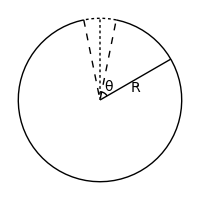

```mathematica
b=0.2;p1={Cos[π/6],Sin[π/6]};
centerPlot@Graphics[{Circle[{0,0},1,{π/2+b,5π/2-b}],Circle[{0,0},0.1,{π/6,π/2}],Line[{{0,0},p1}],Dashed,Line[{{Cos[π/2+b],Sin[π/2+b]},{0,0},{Cos[5π/2-b],Sin[5π/2-b]}}],Dashing[Tiny],Line[{{0,0},{0,1}}],Circle[{0,0},1,{π/2-b,π/2+b}],Text[font["R",Italic],p1/2+{0,-0.1}],Text[font@"θ",0.2{Cos[π/3],Sin[π/3]}+{0.01,-0.01}]},ImageSize->200]
```

Note that the distance from the point at angle θ to the middle of the aperture equals 2R Sin[θ/2] (which can either be found through the Law of Cosines or simple geometry). Therefore, the electric field in the middle of the aperture (which only has a component in the vertical direction) has magnitude

E=∫_0^(2π) ∫_(b/R)^π (k (R^2 Sin[θ]σ))/(4 R^2 Sin[θ/2]^2)Sin[θ/2]ⅆθⅆϕ
=(π k σ)/2∫_(b/R)^π Sin[θ]/Sin[θ/2]ⅆθ
=π k σ∫_(b/R)^π Cos[θ/2]ⅆθ
=2π k σ (Sin[θ/2])_(θ=b/R)^(θ=π)
=2π k σ (1-Sin[b/(2R)])

In the limit b≪R, Sin[b/(2R)]≈b/(2R)≈0 so that E≈2π k σ=σ/(2 ϵ_0), as desired. You are highly encouraged to modify this calculation to compute the electric field at a distance r=R-ϵ and r=R+ϵ from the origin along the line of symmetry of the spherical cap to double check that the electric field is indeed continuous. □

#### A Plane and a Slab

Example
An infinite plane has uniform surface charge density σ. Adjacent to it is an infinite parallel layer of charge of thickness d and uniform volume charge density ρ. All charges are fixed. Find E everywhere.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
We will analyze the sheet and the slab separately, and then combine them using the Principle of Superposition.

We already know that the sheet has an electric field σ/(2 ϵ_0) pointing away at all points in space. How can we determine the electric field from the slab?

There are many ways to compute the slab’s electric field: considering it as a conglomeration of thin sheets, straight up integration, and Gauss’s Law name three distinct methods. We will use Gauss’s Law (but you are invited to check the other methods).

Assume that the slab stretches infinitely far in the y- and z-directions, and that it spans from x=-d/2 to x=d/2. We use a Gaussian cylinder with length 2x centered around x=0 and cross sectional area A in the y-z plane. (Note that the Gaussian cylinder must be centered around the middle of the slab, although it does not need to by a cylinder and can instead be any prism shape.) Gauss’s Law yields 2E A=1/ϵ_0(2|x| A ρ) for |x|≤d/2 and 2E A=1/ϵ_0(d A ρ) for |x|≥d/2. In other words,

E=Piecewise[{{(|x| ρ)/ϵ_0, |x|≤d/2}, {(d ρ)/(2 ϵ_0), |x|>d/2}}]

with the direction +x̂ for points x≥0 and -x̂ for points x<0.

All that remains is to add together the contribution of the electric field from the sheet and the slab (noting the directions of the fields!) to yield the final answer. The following Manipulate shows E as a function of x for various values of (ρ d)/σ.

```mathematica
centerPlot@DynamicModule[{d=1,σ=1,ϵ0=1,ρ},
Manipulate[
ρ=ratio σ/d;
Show[Plot[Piecewise[{{-σ/(2ϵ0),x<-d/2},{σ/(2ϵ0),-d/2<x}}]+Piecewise[{{-(d ρ)/(2ϵ0),x<-d/2},{(x ρ)/ϵ0,-d/2<x<d/2},{(d ρ)/(2ϵ0),x>d/2}}],{x,-d,d},Ticks->{{{-d/2,font@"-d/2"},{d/2,font@"d/2"}},None},AxesLabel->(font[#,Italic]&/@{"x","E"})],Plot[σ/(2ϵ0)-(d ρ)/(2ϵ0),{x,-d/2,d},PlotStyle->{Dashed,ColorData[97,2]}],Graphics[{Arrowheads[{-.02,.02}],Arrow[{{-d/4,-σ/(2ϵ0)-(d ρ)/(2ϵ0)},{-d/4,σ/(2ϵ0)-(d ρ)/(2ϵ0)}}],Arrow[{{6d/8,σ/(2ϵ0)-(d ρ)/(2ϵ0)},{6d/8,σ/(2ϵ0)+(d ρ)/(2ϵ0)}}],Text[font@"σ/ϵ_0",{-d/4,-(d ρ)/(2 ϵ0)}+{0.1,0}],Text[font@"(ρ d)/ϵ_0",{(3 d)/4,σ/(2 ϵ0)}+{0.1,0}]}]]
,{{ratio,2,font@"(ρ d)/σ"},0,5,Appearance->"Open"}]
]
```

Note that there is only a discontinuity in the electric field at x=-d/2 where the sheet of charge resides. There is no discontinuity for the slab of charge. □

#### Advanced Section: Maximum Field from a Blob

Example
1. A point charge is placed somewhere on the curve shown below. This point charge creates an electric field at the origin. Let E_y be the vertical component of this field.What shape (up to a scaling factor) should the curve take so that E_y is independent of the position of the point charge on the curve?
2. You have a moldable material with uniform volume charge density. What shape should the material take if you want to create the largest possible electric field at a given point in space?

Solution
1. Label the points on the curve by their distance r from the origin and an angle θ from the line that this distance subtends with the y-axis.

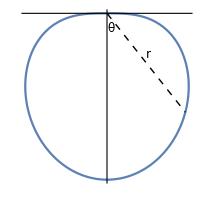

```mathematica
p1={1/2^(1/4)1/(√2),-1/2^(1/4)1/(√2)};
ft=12;
Show[PolarPlot[√Cos[θ+π/2],{θ,0,2π},Ticks->None],Graphics[{Dashed,Line[{{0,0},p1}],Text[Style["r",ft],p1/2+{0.02,0.05}],Text[Style["θ",ft],{0.03,-0.09}]}],ImageSize->200]
```

Then a point charge q on the curve provides a y component of the electric field at the origin equal to

E_y=(k q)/r^2 Cos[θ]

If we want for this to be independent of the charge’s location on the curve, then we must have r^2∝Cos[θ]. Therefore, the curve must have the form

r^2=c^2 Cos[θ]

or equivalently

r=c √Cos[θ]

for some constant c. (We have chosen the positive square root. The negative square root would also work, and it would yield the same curve reflected about the x-axis. Therefore, we only need one of these curves.) This yields a family of curves indexed by c. Note that we ignore the points at r=0 at θ=π/2 and θ=(3π)/2.

2. Assume that the material has been shaped and positioned so that the electric field at the origin takes on the maximum possible value. Assume that the field points in the y-direction. Then all the small elements of charge ⅆq on the surface of the material must give equal contributions to the y component of the field at the origin. This is true because if it weren’t the case, then we could simply move a tiny piece of the material from one point on the surface to another, thereby increasing the field at the origin and contradicting our assumption that the field at the origin is maximum. From Part 1, any vertical cross section (formed by the intersection of the surface with a plane containing the y-axis) must therefore look like the r=c √Cos[θ] curve we found. Equivalently, the desired shape of the material is obtained by forming the surface of revolution of the r=c √Cos[θ] curve about the y-axis with c taking the greatest possible value it can attain to use up all of the material. □

#### Advanced Section: Ball in a Sphere

Example
We know that if a point charge q is located at radius a in the interior of a sphere with radius R and uniform volume charge density ρ, then the force on the point charge is effectively due only to the charge that is located inside radius a.
1. Consider instead a uniform ball of charge located entirely inside a larger sphere of radius R. Let the ball’s radius be b, and let its center be located at radius a in the larger sphere. Its volume charge density is such that its total charge is q. Assume that the ball is superposed on top of the sphere, so that all of the sphere’s charge is still present. Can the force on the ball be obtained by treating it like a point charge and considering only the charge in the larger sphere that is inside radius a?
2. Would the force change if we instead remove the charge in the larger sphere where the ball is? So now we are looking at the force on the ball due to the sphere with a cavity carved out, which is a more realistic scenario.

Solution
1. Gauss’s Law tells us that the electric field inside of a sphere with charge density ρ equals E (4π r^2)=1/ϵ_0(4/3 π r^3 ρ) radially outwards. In other words, E⃗=(r⃗ ρ)/(3 ϵ_0).

The force on the smaller ball due to the larger sphere is found by integrating the effect of the E⃗ field on all the pieces of the ball. The integral is easy to do if we group the pieces in pairs that are symmetrically located on either side of the center of the ball (at position a⃗). Consider two pieces located at positions a⃗+r⃗' and a⃗-r⃗'. Because the above E⃗ field is linear, the r⃗' parts of the sum cancel, and we end up with two pieces effectively located at the center of the ball. We can build up the entire ball from such pairs, so we see that the ball can be effectively treated like a point charge at its center, as far as the force from the larger sphere goes. The force is therefore the same as if it were a point charge of the same charge q. (More generally, if we have an oddly-shaped charged object - instead of a nice ball - located entirely inside of a uniform spherical charge distribution, the force on it is the same as if all of its charge were located at its "center of charge" (which is the analog of the center of mass).)

Alternatively, we could straight up integrate to find the electric field on the ball. Let the large sphere be centered on the origin and the small ball at the point (0,0,a). Assume the large sphere has charge density ρ and the small ball has charge density ρ_2 (where 4/3 π b^3 ρ_2=q).

The force on the small ball (which by symmetry must point in the z-direction) equals

F=∫_0^(2π) ∫_0^π ∫_0^b (ρ √((a+r Cos[θ])^2+(r Sin[θ])^2))/(3 ϵ_0)(a+r Cos[θ])/(√((a+r Cos[θ])^2+(r Sin[θ])^2))(r^2 Sin[θ]ρ_2 ⅆrⅆθⅆϕ)

where the first term is the magnitude of the electric field at the point defined by r, θ, and ϕ; the second term is the component of this electric field in the z-direction; the third term is the unit of charge of the small ball (since force equals electric field times charge). We found the distance √((a+r Cos[θ])^2+(r Sin[θ])^2) between the point at r, θ, and ϕ and the origin using the Law of Cosines.

Evaluating this integral,

F=(2π ρ ρ_2)/(3 ϵ_0)∫_0^b ∫_0^π (a+r Cos[θ])r^2 Sin[θ]ⅆθⅆr
=(2π ρ ρ_2)/(3 ϵ_0)∫_0^b ∫_0^π a r^2 Sin[θ]ⅆθⅆr
=(4π a ρ ρ_2)/(3 ϵ_0)∫_0^b r^2 ⅆr
=(a ρ)/(3 ϵ_0)(4/3 π b^3 ρ_2)

where in the second step we used the fact that ∫_0^π Cos[θ]Sin[θ]ⅆθ=0. The question asks us to compare this electric field to that felt by a point charge q=4/3 π b^3 ρ_2 at a distance a from the center of the sphere. This latter value would indeed equal (a ρ)/(3 ϵ_0)(4/3 π b^3 ρ_2), and it would also point radially outwards from the origin, proving that we can think of the small ball as a point charge q at its center.

2. The situation with the larger sphere plus a cavity is found (using the Principle of Superposition) by simply adding a sphere of charge density -ρ right on top of the small ball. So the total force on the ball would be the force found above plus the force that the ball with charge density -ρ would exert on the ball with charge density ρ. However, the ball with charge density -ρ cannot exert on a force on the ball with charge density ρ, because they are right on top of each other, and by symmetry it is easy to see that the net force must be zero. (Another way to think about it is that an object cannot exert a force on itself, and this new ball with charge density -ρ would exert the opposite force that the ball with charge density ρ exerts on itself; the negative of 0 is 0, so the balls do not exert a net force on each other.)

Note that this exercise is consistent with the result in Problem 1.27, which tells us that the electric field is uniform inside a spherical cavity within a uniform sphere. □

#### Recommended Problems

This is a list of excellent problems (with solutions) in David Morin’s book.

1.6 Zero potential energy for equilibrium

## Mathematica Initialization

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
RawBoxes@CounterBox["TextNumbered","eq1"]
```

TextNumbered